### MonoFrequency (baby step)

0.707107

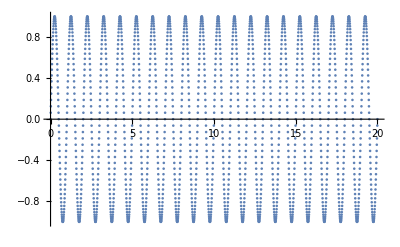

```mathematica
monofrequencydata=Table[{t,Sin[2Pi t]},{t,0,20,0.01}];
StandardDeviation[#[[2]]&/@monofrequencydata]
ListPlot[monofrequencydata]
```

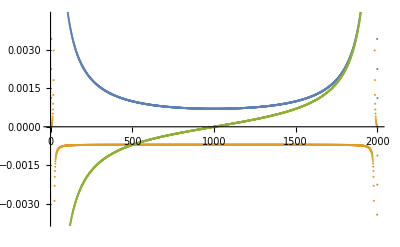

```mathematica
Fourier[#[[2]]&/@monofrequencydata];
ListPlot[{Abs[%],Re[%],Im[%]}]
```

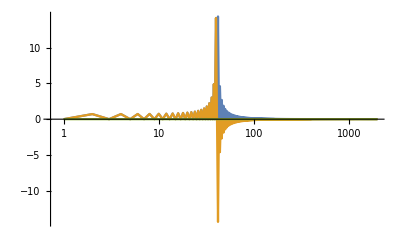

```mathematica
FourierDCT[#[[2]]&/@monofrequencydata];
ListLogLinearPlot[{Abs[%],Re[%],Im[%]},Joined->True,PlotRange->Full]
```

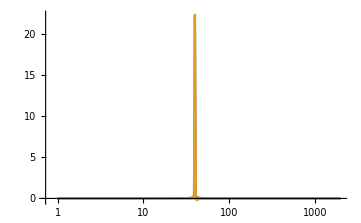

```mathematica
FourierDST[#[[2]]&/@monofrequencydata];
ListLogLinearPlot[{Abs[%],Re[%],Im[%]},Joined->True,PlotRange->Full]
```

```mathematica
PowerSpectralDensity[#[[2]]&/@monofrequencydata,ω]
```

0.4995+2 (0.498515 Cos[ω]+0.495566 Cos[2 ω]+0.490669 Cos[3 ω]+0.483847 Cos[4 ω]+0.475131 Cos[5 ω]+0.46456 Cos[6 ω]+0.452178 Cos[7 ω]+0.438039 Cos[8 ω]+0.422201 Cos[9 ω]+0.40473 Cos[10 ω]+0.385699 Cos[11 ω]+0.365186 Cos[12 ω]+0.343274 Cos[13 ω]+0.320053 Cos[14 ω]+0.295618 Cos[15 ω]+0.270067 Cos[16 ω]+0.243503 Cos[17 ω]+0.216033 Cos[18 ω]+0.187767 Cos[19 ω]+0.158818 Cos[20 ω]+0.129302 Cos[21 ω]+0.0993366 Cos[22 ω]+0.0690408 Cos[23 ω]+0.0385348 Cos[24 ω]+0.00793933 Cos[25 ω]-0.0226248 Cos[26 ω]-0.053037 Cos[27 ω]-0.0831776 Cos[28 ω]-0.112928 Cos[29 ω]-0.142173 Cos[30 ω]-0.170796 Cos[31 ω]-0.198688 Cos[32 ω]-0.225738 Cos[33 ω]-0.251842 Cos[34 ω]-0.2769 Cos[35 ω]-0.300814 Cos[36 ω]-0.323493 Cos[37 ω]-0.344849 Cos[38 ω]-0.364801 Cos[39 ω]-0.383274 Cos[40 ω]-0.400197 Cos[41 ω]-0.415507 Cos[42 ω]-0.429147 Cos[43 ω]-0.441067 Cos[44 ω]-0.451222 Cos[45 ω]-0.459578 Cos[46 ω]-0.466105 Cos[47 ω]-0.47078 Cos[48 ω]-0.473589 Cos[49 ω]-0.474525 Cos[50 ω]-0.473589 Cos[51 ω]-0.470788 Cos[52 ω]-0.466136 Cos[53 ω]-0.459657 Cos[54 ω]-0.451379 Cos[55 ω]-0.441339 Cos[56 ω]-0.42958 Cos[57 ω]-0.416153 Cos[58 ω]-0.401114 Cos[59 ω]-0.384525 Cos[60 ω]-0.366455 Cos[61 ω]-0.34698 Cos[62 ω]-0.326177 Cos[63 ω]-0.304134 Cos[64 ω]-0.280938 Cos[65 ω]-0.256685 Cos[66 ω]-0.231471 Cos[67 ω]-0.205399 Cos[68 ω]-0.178573 Cos[69 ω]-0.1511 Cos[70 ω]-0.123091 Cos[71 ω]-0.0946568 Cos[72 ω]-0.0659106 Cos[73 ω]-0.0369666 Cos[74 ω]-0.00793933 Cos[75 ω]+0.0210566 Cos[76 ω]+0.0499068 Cos[77 ω]+0.0784978 Cos[78 ω]+0.106717 Cos[79 ω]+0.134455 Cos[80 ω]+0.161602 Cos[81 ω]+0.188054 Cos[82 ω]+0.213706 Cos[83 ω]+0.23846 Cos[84 ω]+0.26222 Cos[85 ω]+0.284894 Cos[86 ω]+0.306396 Cos[87 ω]+0.326643 Cos[88 ω]+0.345557 Cos[89 ω]+0.363068 Cos[90 ω]+0.37911 Cos[91 ω]+0.393621 Cos[92 ω]+0.406549 Cos[93 ω]+0.417845 Cos[94 ω]+0.42747 Cos[95 ω]+0.435388 Cos[96 ω]+0.441572 Cos[97 ω]+0.446002 Cos[98 ω]+0.448663 Cos[99 ω]+0.44955 Cos[100 ω]+0.448663 Cos[101 ω]+0.44601 Cos[102 ω]+0.441603 Cos[103 ω]+0.435466 Cos[104 ω]+0.427626 Cos[105 ω]+0.418118 Cos[106 ω]+0.406982 Cos[107 ω]+0.394267 Cos[108 ω]+0.380026 Cos[109 ω]+0.36432 Cos[110 ω]+0.347212 Cos[111 ω]+0.328774 Cos[112 ω]+0.309081 Cos[113 ω]+0.288214 Cos[114 ω]+0.266258 Cos[115 ω]+0.243302 Cos[116 ω]+0.219439 Cos[117 ω]+0.194765 Cos[118 ω]+0.169379 Cos[119 ω]+0.143382 Cos[120 ω]+0.11688 Cos[121 ω]+0.0899769 Cos[122 ω]+0.0627804 Cos[123 ω]+0.0353984 Cos[124 ω]+0.00793933 Cos[125 ω]-0.0194884 Cos[126 ω]-0.0467766 Cos[127 ω]-0.0738179 Cos[128 ω]-0.100506 Cos[129 ω]-0.126737 Cos[130 ω]-0.152409 Cos[131 ω]-0.17742 Cos[132 ω]-0.201674 Cos[133 ω]-0.225078 Cos[134 ω]-0.24754 Cos[135 ω]-0.268975 Cos[136 ω]-0.289299 Cos[137 ω]-0.308437 Cos[138 ω]-0.326314 Cos[139 ω]-0.342863 Cos[140 ω]-0.358022 Cos[141 ω]-0.371735 Cos[142 ω]-0.383951 Cos[143 ω]-0.394624 Cos[144 ω]-0.403717 Cos[145 ω]-0.411197 Cos[146 ω]-0.417039 Cos[147 ω]-0.421224 Cos[148 ω]-0.423738 Cos[149 ω]-0.424575 Cos[150 ω]-0.423738 Cos[151 ω]-0.421231 Cos[152 ω]-0.417071 Cos[153 ω]-0.411276 Cos[154 ω]-0.403873 Cos[155 ω]-0.394896 Cos[156 ω]-0.384384 Cos[157 ω]-0.372381 Cos[158 ω]-0.358939 Cos[159 ω]-0.344114 Cos[160 ω]-0.327968 Cos[161 ω]-0.310568 Cos[162 ω]-0.291984 Cos[163 ω]-0.272294 Cos[164 ω]-0.251578 Cos[165 ω]-0.22992 Cos[166 ω]-0.207407 Cos[167 ω]-0.184131 Cos[168 ω]-0.160185 Cos[169 ω]-0.135665 Cos[170 ω]-0.110669 Cos[171 ω]-0.0852971 Cos[172 ω]-0.0596502 Cos[173 ω]-0.0338302 Cos[174 ω]-0.00793933 Cos[175 ω]+0.0179202 Cos[176 ω]+0.0436464 Cos[177 ω]+0.0691381 Cos[178 ω]+0.0942953 Cos[179 ω]+0.11902 Cos[180 ω]+0.143215 Cos[181 ω]+0.166786 Cos[182 ω]+0.189642 Cos[183 ω]+0.211696 Cos[184 ω]+0.23286 Cos[185 ω]+0.253055 Cos[186 ω]+0.272203 Cos[187 ω]+0.290231 Cos[188 ω]+0.30707 Cos[189 ω]+0.322658 Cos[190 ω]+0.336935 Cos[191 ω]+0.349849 Cos[192 ω]+0.361353 Cos[193 ω]+0.371403 Cos[194 ω]+0.379964 Cos[195 ω]+0.387007 Cos[196 ω]+0.392507 Cos[197 ω]+0.396445 Cos[198 ω]+0.398812 Cos[199 ω]+0.3996 Cos[200 ω]+0.398812 Cos[201 ω]+0.396453 Cos[202 ω]+0.392538 Cos[203 ω]+0.387085 Cos[204 ω]+0.380121 Cos[205 ω]+0.371675 Cos[206 ω]+0.361786 Cos[207 ω]+0.350496 Cos[208 ω]+0.337852 Cos[209 ω]+0.323909 Cos[210 ω]+0.308725 Cos[211 ω]+0.292362 Cos[212 ω]+0.274888 Cos[213 ω]+0.256375 Cos[214 ω]+0.236898 Cos[215 ω]+0.216538 Cos[216 ω]+0.195375 Cos[217 ω]+0.173497 Cos[218 ω]+0.150991 Cos[219 ω]+0.127947 Cos[220 ω]+0.104458 Cos[221 ω]+0.0806172 Cos[222 ω]+0.05652 Cos[223 ω]+0.032262 Cos[224 ω]+0.00793933 Cos[225 ω]-0.016352 Cos[226 ω]-0.0405162 Cos[227 ω]-0.0644582 Cos[228 ω]-0.0880843 Cos[229 ω]-0.111302 Cos[230 ω]-0.134021 Cos[231 ω]-0.156152 Cos[232 ω]-0.177611 Cos[233 ω]-0.198313 Cos[234 ω]-0.21818 Cos[235 ω]-0.237135 Cos[236 ω]-0.255106 Cos[237 ω]-0.272025 Cos[238 ω]-0.287827 Cos[239 ω]-0.302453 Cos[240 ω]-0.315848 Cos[241 ω]-0.327964 Cos[242 ω]-0.338755 Cos[243 ω]-0.348182 Cos[244 ω]-0.356212 Cos[245 ω]-0.362817 Cos[246 ω]-0.367974 Cos[247 ω]-0.371667 Cos[248 ω]-0.373886 Cos[249 ω]-0.374625 Cos[250 ω]-0.373886 Cos[251 ω]-0.371675 Cos[252 ω]-0.368005 Cos[253 ω]-0.362895 Cos[254 ω]-0.356368 Cos[255 ω]-0.348454 Cos[256 ω]-0.339188 Cos[257 ω]-0.32861 Cos[258 ω]-0.316765 Cos[259 ω]-0.303704 Cos[260 ω]-0.289481 Cos[261 ω]-0.274156 Cos[262 ω]-0.257791 Cos[263 ω]-0.240455 Cos[264 ω]-0.222218 Cos[265 ω]-0.203155 Cos[266 ω]-0.183344 Cos[267 ω]-0.162863 Cos[268 ω]-0.141797 Cos[269 ω]-0.120229 Cos[270 ω]-0.0982468 Cos[271 ω]-0.0759374 Cos[272 ω]-0.0533898 Cos[273 ω]-0.0306939 Cos[274 ω]-0.00793933 Cos[275 ω]+0.0147838 Cos[276 ω]+0.037386 Cos[277 ω]+0.0597784 Cos[278 ω]+0.0818732 Cos[279 ω]+0.103584 Cos[280 ω]+0.124827 Cos[281 ω]+0.145518 Cos[282 ω]+0.165579 Cos[283 ω]+0.184931 Cos[284 ω]+0.2035 Cos[285 ω]+0.221216 Cos[286 ω]+0.23801 Cos[287 ω]+0.253819 Cos[288 ω]+0.268583 Cos[289 ω]+0.282247 Cos[290 ω]+0.294761 Cos[291 ω]+0.306078 Cos[292 ω]+0.316156 Cos[293 ω]+0.324961 Cos[294 ω]+0.332459 Cos[295 ω]+0.338626 Cos[296 ω]+0.343441 Cos[297 ω]+0.346889 Cos[298 ω]+0.34896 Cos[299 ω]+0.34965 Cos[300 ω]+0.34896 Cos[301 ω]+0.346897 Cos[302 ω]+0.343473 Cos[303 ω]+0.338705 Cos[304 ω]+0.332615 Cos[305 ω]+0.325233 Cos[306 ω]+0.31659 Cos[307 ω]+0.306724 Cos[308 ω]+0.295678 Cos[309 ω]+0.283499 Cos[310 ω]+0.270237 Cos[311 ω]+0.25595 Cos[312 ω]+0.240695 Cos[313 ω]+0.224535 Cos[314 ω]+0.207538 Cos[315 ω]+0.189773 Cos[316 ω]+0.171312 Cos[317 ω]+0.152229 Cos[318 ω]+0.132603 Cos[319 ω]+0.112512 Cos[320 ω]+0.0920358 Cos[321 ω]+0.0712575 Cos[322 ω]+0.0502596 Cos[323 ω]+0.0291257 Cos[324 ω]+0.00793933 Cos[325 ω]-0.0132156 Cos[326 ω]-0.0342558 Cos[327 ω]-0.0550985 Cos[328 ω]-0.0756622 Cos[329 ω]-0.0958665 Cos[330 ω]-0.115633 Cos[331 ω]-0.134884 Cos[332 ω]-0.153547 Cos[333 ω]-0.171549 Cos[334 ω]-0.18882 Cos[335 ω]-0.205296 Cos[336 ω]-0.220913 Cos[337 ω]-0.235613 Cos[338 ω]-0.24934 Cos[339 ω]-0.262042 Cos[340 ω]-0.273674 Cos[341 ω]-0.284192 Cos[342 ω]-0.293558 Cos[343 ω]-0.301739 Cos[344 ω]-0.308706 Cos[345 ω]-0.314436 Cos[346 ω]-0.318909 Cos[347 ω]-0.322111 Cos[348 ω]-0.324035 Cos[349 ω]-0.324675 Cos[350 ω]-0.324035 Cos[351 ω]-0.322119 Cos[352 ω]-0.31894 Cos[353 ω]-0.314514 Cos[354 ω]-0.308863 Cos[355 ω]-0.302012 Cos[356 ω]-0.293992 Cos[357 ω]-0.284838 Cos[358 ω]-0.274591 Cos[359 ω]-0.263293 Cos[360 ω]-0.250994 Cos[361 ω]-0.237744 Cos[362 ω]-0.223598 Cos[363 ω]-0.208616 Cos[364 ω]-0.192858 Cos[365 ω]-0.176391 Cos[366 ω]-0.15928 Cos[367 ω]-0.141596 Cos[368 ω]-0.123409 Cos[369 ω]-0.104794 Cos[370 ω]-0.0858247 Cos[371 ω]-0.0665777 Cos[372 ω]-0.0471294 Cos[373 ω]-0.0275575 Cos[374 ω]-0.00793933 Cos[375 ω]+0.0116474 Cos[376 ω]+0.0311256 Cos[377 ω]+0.0504187 Cos[378 ω]+0.0694512 Cos[379 ω]+0.0881488 Cos[380 ω]+0.106439 Cos[381 ω]+0.124251 Cos[382 ω]+0.141515 Cos[383 ω]+0.158166 Cos[384 ω]+0.17414 Cos[385 ω]+0.189376 Cos[386 ω]+0.203817 Cos[387 ω]+0.217407 Cos[388 ω]+0.230096 Cos[389 ω]+0.241837 Cos[390 ω]+0.252587 Cos[391 ω]+0.262306 Cos[392 ω]+0.27096 Cos[393 ω]+0.278518 Cos[394 ω]+0.284954 Cos[395 ω]+0.290245 Cos[396 ω]+0.294376 Cos[397 ω]+0.297333 Cos[398 ω]+0.299109 Cos[399 ω]+0.2997 Cos[400 ω]+0.299109 Cos[401 ω]+0.297341 Cos[402 ω]+0.294408 Cos[403 ω]+0.290324 Cos[404 ω]+0.28511 Cos[405 ω]+0.27879 Cos[406 ω]+0.271394 Cos[407 ω]+0.262952 Cos[408 ω]+0.253504 Cos[409 ω]+0.243088 Cos[410 ω]+0.23175 Cos[411 ω]+0.219538 Cos[412 ω]+0.206501 Cos[413 ω]+0.192696 Cos[414 ω]+0.178178 Cos[415 ω]+0.163009 Cos[416 ω]+0.147248 Cos[417 ω]+0.130962 Cos[418 ω]+0.114215 Cos[419 ω]+0.0970762 Cos[420 ω]+0.0796137 Cos[421 ω]+0.0618978 Cos[422 ω]+0.0439992 Cos[423 ω]+0.0259893 Cos[424 ω]+0.00793933 Cos[425 ω]-0.0100792 Cos[426 ω]-0.0279954 Cos[427 ω]-0.0457388 Cos[428 ω]-0.0632401 Cos[429 ω]-0.0804311 Cos[430 ω]-0.097245 Cos[431 ω]-0.113617 Cos[432 ω]-0.129483 Cos[433 ω]-0.144784 Cos[434 ω]-0.15946 Cos[435 ω]-0.173457 Cos[436 ω]-0.18672 Cos[437 ω]-0.199201 Cos[438 ω]-0.210852 Cos[439 ω]-0.221632 Cos[440 ω]-0.2315 Cos[441 ω]-0.240421 Cos[442 ω]-0.248362 Cos[443 ω]-0.255297 Cos[444 ω]-0.261201 Cos[445 ω]-0.266055 Cos[446 ω]-0.269843 Cos[447 ω]-0.272555 Cos[448 ω]-0.274183 Cos[449 ω]-0.274725 Cos[450 ω]-0.274183 Cos[451 ω]-0.272563 Cos[452 ω]-0.269875 Cos[453 ω]-0.266133 Cos[454 ω]-0.261357 Cos[455 ω]-0.255569 Cos[456 ω]-0.248796 Cos[457 ω]-0.241067 Cos[458 ω]-0.232417 Cos[459 ω]-0.222883 Cos[460 ω]-0.212507 Cos[461 ω]-0.201332 Cos[462 ω]-0.189405 Cos[463 ω]-0.176776 Cos[464 ω]-0.163499 Cos[465 ω]-0.149626 Cos[466 ω]-0.135216 Cos[467 ω]-0.120328 Cos[468 ω]-0.105021 Cos[469 ω]-0.0893585 Cos[470 ω]-0.0734027 Cos[471 ω]-0.057218 Cos[472 ω]-0.040869 Cos[473 ω]-0.0244211 Cos[474 ω]-0.00793933 Cos[475 ω]+0.00851101 Cos[476 ω]+0.0248652 Cos[477 ω]+0.041059 Cos[478 ω]+0.0570291 Cos[479 ω]+0.0727134 Cos[480 ω]+0.0880511 Cos[481 ω]+0.102983 Cos[482 ω]+0.117452 Cos[483 ω]+0.131402 Cos[484 ω]+0.14478 Cos[485 ω]+0.157537 Cos[486 ω]+0.169623 Cos[487 ω]+0.180995 Cos[488 ω]+0.191609 Cos[489 ω]+0.201427 Cos[490 ω]+0.210413 Cos[491 ω]+0.218535 Cos[492 ω]+0.225764 Cos[493 ω]+0.232076 Cos[494 ω]+0.237448 Cos[495 ω]+0.241865 Cos[496 ω]+0.245311 Cos[497 ω]+0.247777 Cos[498 ω]+0.249257 Cos[499 ω]+0.24975 Cos[500 ω]+0.249257 Cos[501 ω]+0.247785 Cos[502 ω]+0.245342 Cos[503 ω]+0.241943 Cos[504 ω]+0.237605 Cos[505 ω]+0.232348 Cos[506 ω]+0.226197 Cos[507 ω]+0.219181 Cos[508 ω]+0.21133 Cos[509 ω]+0.202678 Cos[510 ω]+0.193263 Cos[511 ω]+0.183126 Cos[512 ω]+0.172308 Cos[513 ω]+0.160857 Cos[514 ω]+0.148819 Cos[515 ω]+0.136244 Cos[516 ω]+0.123185 Cos[517 ω]+0.109694 Cos[518 ω]+0.0958273 Cos[519 ω]+0.0816407 Cos[520 ω]+0.0671916 Cos[521 ω]+0.0525381 Cos[522 ω]+0.0377388 Cos[523 ω]+0.0228529 Cos[524 ω]+0.00793933 Cos[525 ω]-0.00694282 Cos[526 ω]-0.021735 Cos[527 ω]-0.0363791 Cos[528 ω]-0.0508181 Cos[529 ω]-0.0649957 Cos[530 ω]-0.0788572 Cos[531 ω]-0.0923491 Cos[532 ω]-0.10542 Cos[533 ω]-0.11802 Cos[534 ω]-0.1301 Cos[535 ω]-0.141617 Cos[536 ω]-0.152527 Cos[537 ω]-0.162789 Cos[538 ω]-0.172365 Cos[539 ω]-0.181221 Cos[540 ω]-0.189326 Cos[541 ω]-0.196649 Cos[542 ω]-0.203166 Cos[543 ω]-0.208855 Cos[544 ω]-0.213696 Cos[545 ω]-0.217674 Cos[546 ω]-0.220778 Cos[547 ω]-0.222999 Cos[548 ω]-0.224332 Cos[549 ω]-0.224775 Cos[550 ω]-0.224332 Cos[551 ω]-0.223007 Cos[552 ω]-0.22081 Cos[553 ω]-0.217753 Cos[554 ω]-0.213852 Cos[555 ω]-0.209127 Cos[556 ω]-0.203599 Cos[557 ω]-0.197295 Cos[558 ω]-0.190242 Cos[559 ω]-0.182473 Cos[560 ω]-0.174019 Cos[561 ω]-0.164919 Cos[562 ω]-0.155212 Cos[563 ω]-0.144937 Cos[564 ω]-0.134139 Cos[565 ω]-0.122862 Cos[566 ω]-0.111153 Cos[567 ω]-0.0990602 Cos[568 ω]-0.0866334 Cos[569 ω]-0.073923 Cos[570 ω]-0.0609806 Cos[571 ω]-0.0478582 Cos[572 ω]-0.0346086 Cos[573 ω]-0.0212847 Cos[574 ω]-0.00793933 Cos[575 ω]+0.00537463 Cos[576 ω]+0.0186048 Cos[577 ω]+0.0316993 Cos[578 ω]+0.044607 Cos[579 ω]+0.057278 Cos[580 ω]+0.0696632 Cos[581 ω]+0.0817152 Cos[582 ω]+0.093388 Cos[583 ω]+0.104637 Cos[584 ω]+0.115421 Cos[585 ω]+0.125698 Cos[586 ω]+0.13543 Cos[587 ω]+0.144583 Cos[588 ω]+0.153122 Cos[589 ω]+0.161016 Cos[590 ω]+0.168238 Cos[591 ω]+0.174763 Cos[592 ω]+0.180568 Cos[593 ω]+0.185633 Cos[594 ω]+0.189943 Cos[595 ω]+0.193484 Cos[596 ω]+0.196245 Cos[597 ω]+0.198221 Cos[598 ω]+0.199406 Cos[599 ω]+0.1998 Cos[600 ω]+0.199406 Cos[601 ω]+0.198229 Cos[602 ω]+0.196277 Cos[603 ω]+0.193562 Cos[604 ω]+0.190099 Cos[605 ω]+0.185906 Cos[606 ω]+0.181001 Cos[607 ω]+0.175409 Cos[608 ω]+0.169155 Cos[609 ω]+0.162267 Cos[610 ω]+0.154776 Cos[611 ω]+0.146713 Cos[612 ω]+0.138115 Cos[613 ω]+0.129017 Cos[614 ω]+0.119459 Cos[615 ω]+0.109479 Cos[616 ω]+0.099121 Cos[617 ω]+0.0884263 Cos[618 ω]+0.0774395 Cos[619 ω]+0.0662053 Cos[620 ω]+0.0547696 Cos[621 ω]+0.0431784 Cos[622 ω]+0.0314784 Cos[623 ω]+0.0197165 Cos[624 ω]+0.00793933 Cos[625 ω]-0.00380643 Cos[626 ω]-0.0154746 Cos[627 ω]-0.0270194 Cos[628 ω]-0.038396 Cos[629 ω]-0.0495603 Cos[630 ω]-0.0604693 Cos[631 ω]-0.0710814 Cos[632 ω]-0.0813562 Cos[633 ω]-0.0912549 Cos[634 ω]-0.100741 Cos[635 ω]-0.109778 Cos[636 ω]-0.118334 Cos[637 ω]-0.126377 Cos[638 ω]-0.133878 Cos[639 ω]-0.140811 Cos[640 ω]-0.147151 Cos[641 ω]-0.152877 Cos[642 ω]-0.15797 Cos[643 ω]-0.162412 Cos[644 ω]-0.16619 Cos[645 ω]-0.169294 Cos[646 ω]-0.171713 Cos[647 ω]-0.173443 Cos[648 ω]-0.17448 Cos[649 ω]-0.174825 Cos[650 ω]-0.17448 Cos[651 ω]-0.173451 Cos[652 ω]-0.171744 Cos[653 ω]-0.169372 Cos[654 ω]-0.166347 Cos[655 ω]-0.162684 Cos[656 ω]-0.158403 Cos[657 ω]-0.153524 Cos[658 ω]-0.148068 Cos[659 ω]-0.142062 Cos[660 ω]-0.135532 Cos[661 ω]-0.128507 Cos[662 ω]-0.121018 Cos[663 ω]-0.113098 Cos[664 ω]-0.104779 Cos[665 ω]-0.0960971 Cos[666 ω]-0.0870891 Cos[667 ω]-0.0777925 Cos[668 ω]-0.0682456 Cos[669 ω]-0.0584876 Cos[670 ω]-0.0485585 Cos[671 ω]-0.0384985 Cos[672 ω]-0.0283482 Cos[673 ω]-0.0181483 Cos[674 ω]-0.00793933 Cos[675 ω]+0.00223824 Cos[676 ω]+0.0123444 Cos[677 ω]+0.0223395 Cos[678 ω]+0.0321849 Cos[679 ω]+0.0418426 Cos[680 ω]+0.0512754 Cos[681 ω]+0.0604476 Cos[682 ω]+0.0693244 Cos[683 ω]+0.0778727 Cos[684 ω]+0.0860606 Cos[685 ω]+0.0938582 Cos[686 ω]+0.101237 Cos[687 ω]+0.108171 Cos[688 ω]+0.114634 Cos[689 ω]+0.120606 Cos[690 ω]+0.126064 Cos[691 ω]+0.130992 Cos[692 ω]+0.135372 Cos[693 ω]+0.139191 Cos[694 ω]+0.142438 Cos[695 ω]+0.145103 Cos[696 ω]+0.14718 Cos[697 ω]+0.148665 Cos[698 ω]+0.149554 Cos[699 ω]+0.14985 Cos[700 ω]+0.149554 Cos[701 ω]+0.148672 Cos[702 ω]+0.147212 Cos[703 ω]+0.145182 Cos[704 ω]+0.142594 Cos[705 ω]+0.139463 Cos[706 ω]+0.135805 Cos[707 ω]+0.131638 Cos[708 ω]+0.126981 Cos[709 ω]+0.121857 Cos[710 ω]+0.116289 Cos[711 ω]+0.110301 Cos[712 ω]+0.103922 Cos[713 ω]+0.0971779 Cos[714 ω]+0.0900988 Cos[715 ω]+0.0827148 Cos[716 ω]+0.0750573 Cos[717 ω]+0.0671586 Cos[718 ω]+0.0590516 Cos[719 ω]+0.0507699 Cos[720 ω]+0.0423475 Cos[721 ω]+0.0338187 Cos[722 ω]+0.025218 Cos[723 ω]+0.0165801 Cos[724 ω]+0.00793933 Cos[725 ω]-0.000670041 Cos[726 ω]-0.00921417 Cos[727 ω]-0.0176597 Cos[728 ω]-0.0259739 Cos[729 ω]-0.0341249 Cos[730 ω]-0.0420815 Cos[731 ω]-0.0498137 Cos[732 ω]-0.0572926 Cos[733 ω]-0.0644904 Cos[734 ω]-0.0713807 Cos[735 ω]-0.0779385 Cos[736 ω]-0.0841405 Cos[737 ω]-0.0899646 Cos[738 ω]-0.0953908 Cos[739 ω]-0.100401 Cos[740 ω]-0.104977 Cos[741 ω]-0.109106 Cos[742 ω]-0.112774 Cos[743 ω]-0.11597 Cos[744 ω]-0.118685 Cos[745 ω]-0.120913 Cos[746 ω]-0.122648 Cos[747 ω]-0.123887 Cos[748 ω]-0.124629 Cos[749 ω]-0.124875 Cos[750 ω]-0.124629 Cos[751 ω]-0.123894 Cos[752 ω]-0.122679 Cos[753 ω]-0.120991 Cos[754 ω]-0.118841 Cos[755 ω]-0.116242 Cos[756 ω]-0.113207 Cos[757 ω]-0.109752 Cos[758 ω]-0.105894 Cos[759 ω]-0.101652 Cos[760 ω]-0.0970451 Cos[761 ω]-0.0920955 Cos[762 ω]-0.0868253 Cos[763 ω]-0.0812583 Cos[764 ω]-0.0754188 Cos[765 ω]-0.0693325 Cos[766 ω]-0.0630255 Cos[767 ω]-0.0565248 Cos[768 ω]-0.0498577 Cos[769 ω]-0.0430522 Cos[770 ω]-0.0361364 Cos[771 ω]-0.0291388 Cos[772 ω]-0.0220878 Cos[773 ω]-0.0150119 Cos[774 ω]-0.00793933 Cos[775 ω]-0.000898154 Cos[776 ω]+0.00608397 Cos[777 ω]+0.0129798 Cos[778 ω]+0.0197629 Cos[779 ω]+0.0264072 Cos[780 ω]+0.0328876 Cos[781 ω]+0.0391799 Cos[782 ω]+0.0452608 Cos[783 ω]+0.0511081 Cos[784 ω]+0.0567007 Cos[785 ω]+0.0620189 Cos[786 ω]+0.0670439 Cos[787 ω]+0.0717586 Cos[788 ω]+0.0761472 Cos[789 ω]+0.0801953 Cos[790 ω]+0.08389 Cos[791 ω]+0.08722 Cos[792 ω]+0.0901756 Cos[793 ω]+0.0927486 Cos[794 ω]+0.0949325 Cos[795 ω]+0.0967224 Cos[796 ω]+0.0981149 Cos[797 ω]+0.0991084 Cos[798 ω]+0.099703 Cos[799 ω]+0.0999001 Cos[800 ω]+0.099703 Cos[801 ω]+0.0991163 Cos[802 ω]+0.0981463 Cos[803 ω]+0.0968008 Cos[804 ω]+0.0950888 Cos[805 ω]+0.0930209 Cos[806 ω]+0.090609 Cos[807 ω]+0.0878662 Cos[808 ω]+0.0848069 Cos[809 ω]+0.0814465 Cos[810 ω]+0.0778015 Cos[811 ω]+0.0738894 Cos[812 ω]+0.0697287 Cos[813 ω]+0.0653386 Cos[814 ω]+0.0607389 Cos[815 ω]+0.0559502 Cos[816 ω]+0.0509937 Cos[817 ω]+0.0458909 Cos[818 ω]+0.0406638 Cos[819 ω]+0.0353345 Cos[820 ω]+0.0299254 Cos[821 ω]+0.024459 Cos[822 ω]+0.0189576 Cos[823 ω]+0.0134437 Cos[824 ω]+0.00793933 Cos[825 ω]+0.00246635 Cos[826 ω]-0.00295377 Cos[827 ω]-0.00829999 Cos[828 ω]-0.0135518 Cos[829 ω]-0.0186894 Cos[830 ω]-0.0236936 Cos[831 ω]-0.028546 Cos[832 ω]-0.033229 Cos[833 ω]-0.0377258 Cos[834 ω]-0.0420208 Cos[835 ω]-0.0460992 Cos[836 ω]-0.0499473 Cos[837 ω]-0.0535526 Cos[838 ω]-0.0569036 Cos[839 ω]-0.0599901 Cos[840 ω]-0.0628029 Cos[841 ω]-0.0653343 Cos[842 ω]-0.0675776 Cos[843 ω]-0.0695275 Cos[844 ω]-0.0711799 Cos[845 ω]-0.072532 Cos[846 ω]-0.0735822 Cos[847 ω]-0.0743303 Cos[848 ω]-0.0747772 Cos[849 ω]-0.0749251 Cos[850 ω]-0.0747772 Cos[851 ω]-0.0743382 Cos[852 ω]-0.0736137 Cos[853 ω]-0.0726104 Cos[854 ω]-0.0713361 Cos[855 ω]-0.0697997 Cos[856 ω]-0.0680109 Cos[857 ω]-0.0659804 Cos[858 ω]-0.0637198 Cos[859 ω]-0.0612412 Cos[860 ω]-0.0585579 Cos[861 ω]-0.0556834 Cos[862 ω]-0.0526322 Cos[863 ω]-0.0494189 Cos[864 ω]-0.0460589 Cos[865 ω]-0.0425679 Cos[866 ω]-0.0389619 Cos[867 ω]-0.0352571 Cos[868 ω]-0.0314699 Cos[869 ω]-0.0276168 Cos[870 ω]-0.0237144 Cos[871 ω]-0.0197791 Cos[872 ω]-0.0158274 Cos[873 ω]-0.0118755 Cos[874 ω]-0.00793933 Cos[875 ω]-0.00403454 Cos[876 ω]-0.000176436 Cos[877 ω]+0.00362014 Cos[878 ω]+0.0073408 Cos[879 ω]+0.0109717 Cos[880 ω]+0.0144997 Cos[881 ω]+0.0179122 Cos[882 ω]+0.0211971 Cos[883 ω]+0.0243435 Cos[884 ω]+0.0273408 Cos[885 ω]+0.0301795 Cos[886 ω]+0.0328507 Cos[887 ω]+0.0353466 Cos[888 ω]+0.03766 Cos[889 ω]+0.0397849 Cos[890 ω]+0.0417158 Cos[891 ω]+0.0434485 Cos[892 ω]+0.0449795 Cos[893 ω]+0.0463063 Cos[894 ω]+0.0474272 Cos[895 ω]+0.0483416 Cos[896 ω]+0.0490496 Cos[897 ω]+0.0495522 Cos[898 ω]+0.0498515 Cos[899 ω]+0.04995 Cos[900 ω]+0.0498515 Cos[901 ω]+0.0495601 Cos[902 ω]+0.049081 Cos[903 ω]+0.04842 Cos[904 ω]+0.0475834 Cos[905 ω]+0.0465785 Cos[906 ω]+0.0454128 Cos[907 ω]+0.0440946 Cos[908 ω]+0.0426326 Cos[909 ω]+0.041036 Cos[910 ω]+0.0393143 Cos[911 ω]+0.0374774 Cos[912 ω]+0.0355356 Cos[913 ω]+0.0334992 Cos[914 ω]+0.031379 Cos[915 ω]+0.0291856 Cos[916 ω]+0.0269301 Cos[917 ω]+0.0246232 Cos[918 ω]+0.022276 Cos[919 ω]+0.0198991 Cos[920 ω]+0.0175033 Cos[921 ω]+0.0150993 Cos[922 ω]+0.0126972 Cos[923 ω]+0.0103073 Cos[924 ω]+0.00793933 Cos[925 ω]+0.00560274 Cos[926 ω]+0.00330664 Cos[927 ω]+0.00105972 Cos[928 ω]-0.00112977 Cos[929 ω]-0.00325404 Cos[930 ω]-0.0053058 Cos[931 ω]-0.00727831 Cos[932 ω]-0.00916533 Cos[933 ω]-0.0109612 Cos[934 ω]-0.0126609 Cos[935 ω]-0.0142598 Cos[936 ω]-0.0157542 Cos[937 ω]-0.0171406 Cos[938 ω]-0.0184165 Cos[939 ω]-0.0195796 Cos[940 ω]-0.0206287 Cos[941 ω]-0.0215627 Cos[942 ω]-0.0223814 Cos[943 ω]-0.0230851 Cos[944 ω]-0.0236745 Cos[945 ω]-0.0241512 Cos[946 ω]-0.0245169 Cos[947 ω]-0.0247742 Cos[948 ω]-0.0249257 Cos[949 ω]-0.024975 Cos[950 ω]-0.0249257 Cos[951 ω]-0.024782 Cos[952 ω]-0.0245484 Cos[953 ω]-0.0242296 Cos[954 ω]-0.0238308 Cos[955 ω]-0.0233573 Cos[956 ω]-0.0228148 Cos[957 ω]-0.0222089 Cos[958 ω]-0.0215455 Cos[959 ω]-0.0208308 Cos[960 ω]-0.0200707 Cos[961 ω]-0.0192714 Cos[962 ω]-0.018439 Cos[963 ω]-0.0175795 Cos[964 ω]-0.016699 Cos[965 ω]-0.0158034 Cos[966 ω]-0.0148983 Cos[967 ω]-0.0139894 Cos[968 ω]-0.013082 Cos[969 ω]-0.0121814 Cos[970 ω]-0.0112923 Cos[971 ω]-0.0104194 Cos[972 ω]-0.00956704 Cos[973 ω]-0.00873913 Cos[974 ω]-0.00793933 Cos[975 ω]-0.00717093 Cos[976 ω]-0.00643684 Cos[977 ω]-0.00573957 Cos[978 ω]-0.00508127 Cos[979 ω]-0.00446367 Cos[980 ω]-0.00388812 Cos[981 ω]-0.00335554 Cos[982 ω]-0.00286648 Cos[983 ω]-0.00242107 Cos[984 ω]-0.00201907 Cos[985 ω]-0.00165985 Cos[986 ω]-0.00134241 Cos[987 ω]-0.00106541 Cos[988 ω]-0.000827132 Cos[989 ω]-0.000625579 Cos[990 ω]-0.000458427 Cos[991 ω]-0.000323078 Cos[992 ω]-0.000216673 Cos[993 ω]-0.000136121 Cos[994 ω]-0.0000781228 Cos[995 ω]-0.0000392008 Cos[996 ω]-0.0000157238 Cos[997 ω]-3.93871×10^-6 Cos[998 ω]+6.5903×10^-17 Cos[999 ω]+3.20686×10^-17 Cos[1000 ω])

```mathematica
homebrewPSDfunc1[list_,delay_]:=1/Length[list]Total[Table[list[[If[i+delay>Length[list],Mod[i+delay,Length[list]],i],2]]*list[[i,2]],{i,1,Length[list],1}]]
```

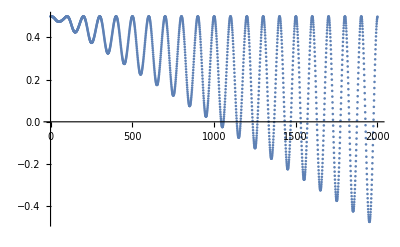

```mathematica
ListPlot[Table[{i,homebrewPSDfunc1[monofrequencydata,i]},{i,0,Length[monofrequencydata]-1}]]
```

### MonoFrequency (baby step + randomize time)

0.712101

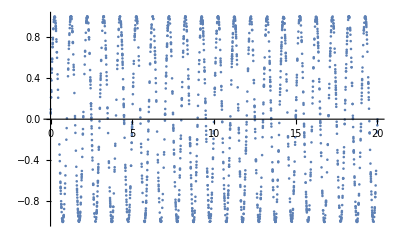

```mathematica
monofrequencydata=Table[t=RandomReal[{0,20}];{t,Sin[2Pi t]},{i,1,2000}];
StandardDeviation[#[[2]]&/@monofrequencydata]
ListPlot[monofrequencydata]
```

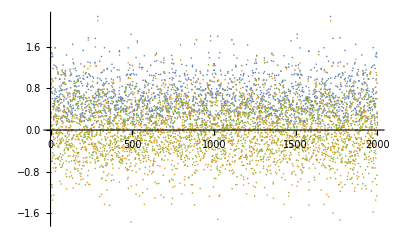

```mathematica
Fourier[#[[2]]&/@monofrequencydata];
ListPlot[{Abs[%],Re[%],Im[%]}]
```

```mathematica
FourierDCT[#[[2]]&/@monofrequencydata];
ListLogLinearPlot[{Abs[%],Re[%],Im[%]},Joined->True,PlotRange->Full]
```

-Graphics-

```mathematica
FourierDST[#[[2]]&/@monofrequencydata];
ListLogLinearPlot[{Abs[%],Re[%],Im[%]},Joined->True,PlotRange->Full]
```

-Graphics-

```mathematica
PowerSpectralDensity[#[[2]]&/@monofrequencydata,ω]
```

0.506834+2 (0.0189522 Cos[ω]+0.0165967 Cos[2 ω]+0.00148803 Cos[3 ω]+2995+0.000529998 Cos[1998 ω]-0.000214763 Cos[1999 ω])
 |  |  |  |

```mathematica
homebrewPSDfunc1[list_,delay_]:=1/Length[list]Total[Table[list[[If[i+delay>Length[list],Mod[i+delay,Length[list]],i],2]]*list[[i,2]],{i,1,Length[list],1}]]
```

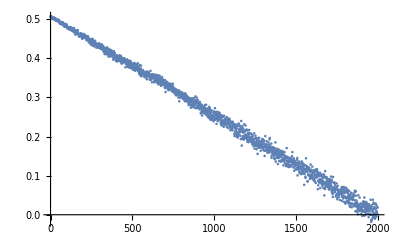

```mathematica
ListPlot[Table[{i,homebrewPSDfunc1[monofrequencydata,i]},{i,0,Length[monofrequencydata]-1}]]
```